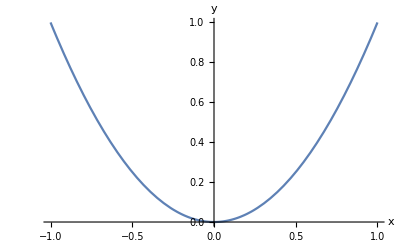

```mathematica
Plot[x^2,{x,-1,1},AxesLabel-> {"x","y"}]
```

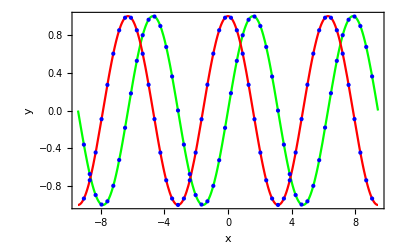

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},Axes-> True,Frame-> True,Mesh->50,MeshStyle-> Blue, PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},AxesLabel->{"x","y"}]
```

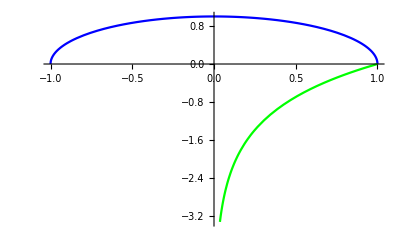

```mathematica
Plot[{√(1-x^2),Log[x]},{x,-1,1},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0]}]
```

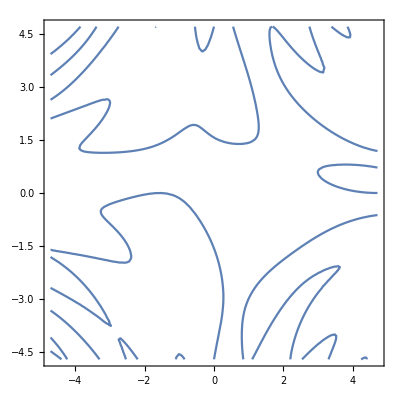

```mathematica
ContourPlot[Sin[x y]==Sin[x]+Cos[y],{x,-(3π)/2,(3π)/2},{y,-(3π)/2,(3π)/2}]
```

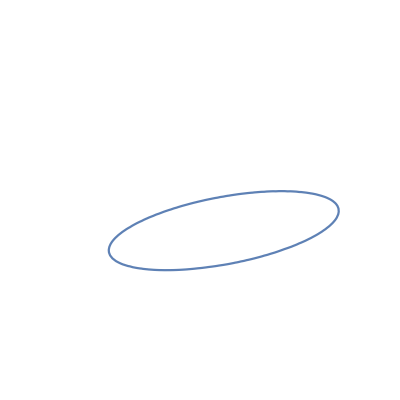

```mathematica
ContourPlot[x^2+16 y^2-4x y+22x+46y+9==0,{x,-50,5},{y,-20,20},Frame-> False]
```

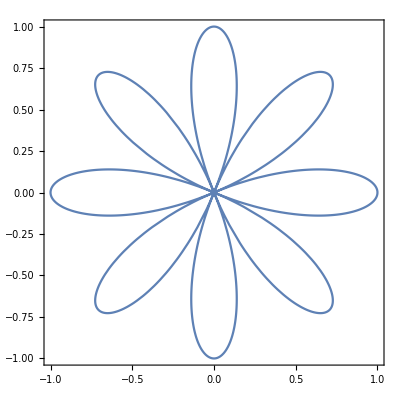

```mathematica
PolarPlot[Cos[4θ],{θ,0,2π},Axes-> False,Frame->True]
```

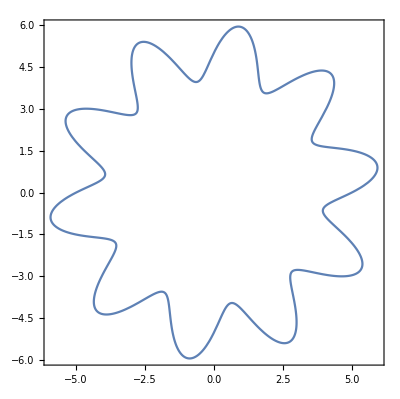

```mathematica
PolarPlot[5+Sin[10θ],{θ,0,2π},Axes-> False,Frame->True]
```

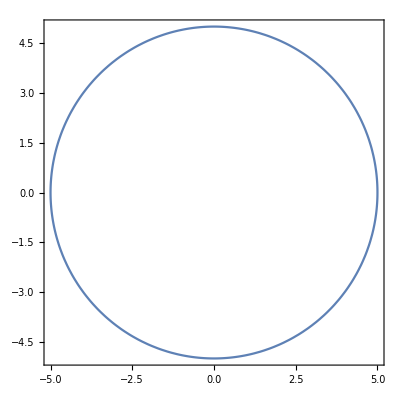

```mathematica
ParametricPlot[{5Cos[θ],5Sin[θ]},{θ,0,2π},Axes-> False,Frame->True]
```

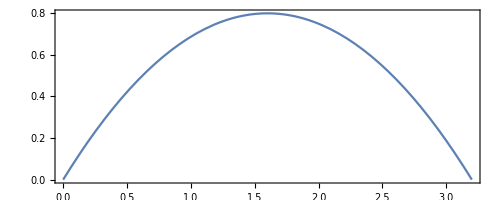

```mathematica
ParametricPlot[{4t,4t-5 t^2},{t,0,4/5},Axes-> False,Frame->True]
```

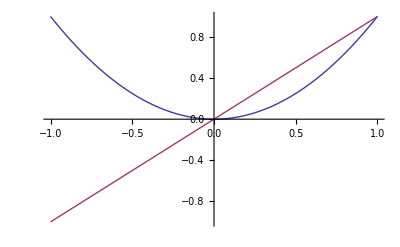

```mathematica
Plot[{x^2,x},{x,-1,1}]
```

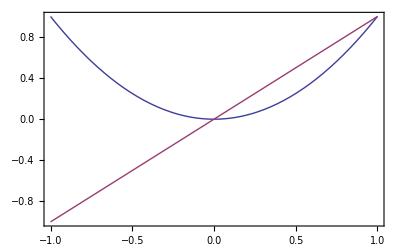

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> False,Frame-> True]
```

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> True,Frame-> True]
```

-Graphics-

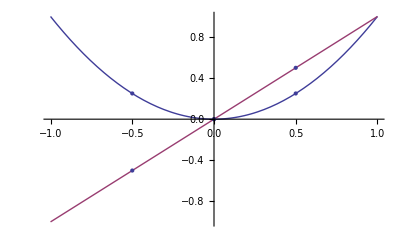

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> True,Frame-> False,Mesh-> 3]
```

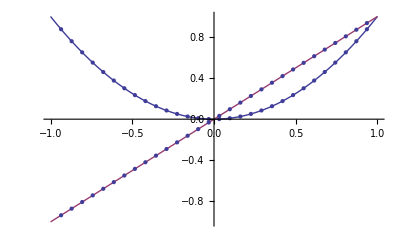

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> True,Frame-> False,Mesh-> 30]
```

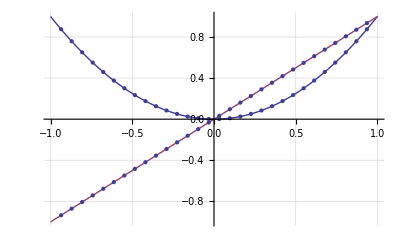

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> Automatic]
```

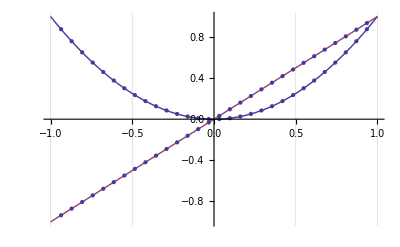

```mathematica
Plot[{x^2,x},{x,-1,1},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {Automatic,None}]
```

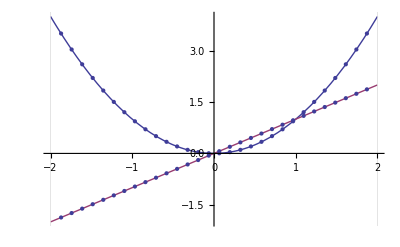

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None}]
```

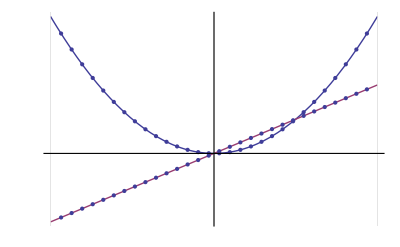

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> None]
```

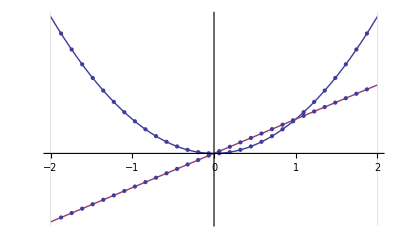

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None}]
```

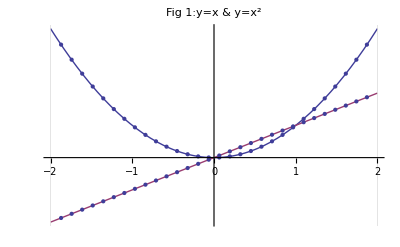

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2"]
```

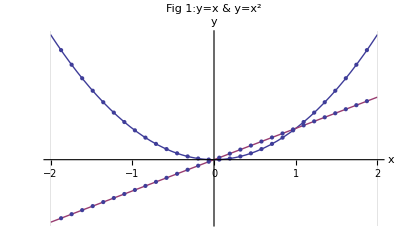

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"}]
```

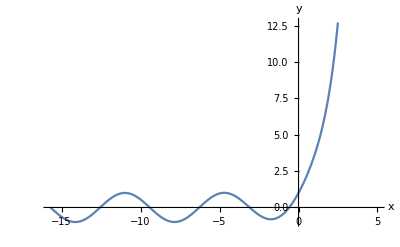

```mathematica
Plot[{E^x+Sin[x]},{x,-5π,5},AxesLabel-> {"x","y"}]
```

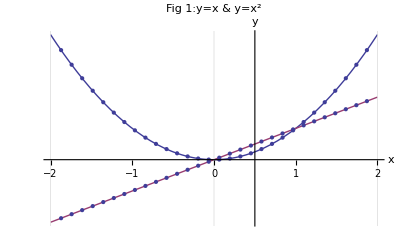

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0}]
```

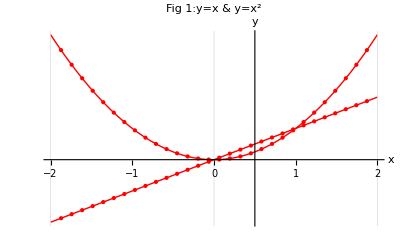

```mathematica
Plot[{x^2,x},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0},PlotStyle-> RGBColor[1,0,0]]
```

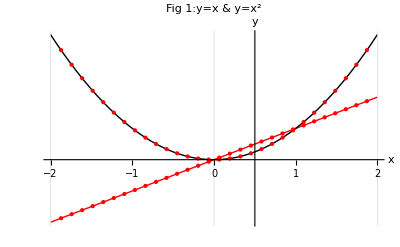

```mathematica
Plot[{x,x^2},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0},PlotStyle-> {RGBColor[1,0,0],RGBColor[0,0,0]}]
```

```mathematica
Plot[{x,x^2},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0},PlotStyle-> {RGBColor[1,0,0],RGBColor[0,0,0]},PlotLegend-> {"x","x^2"}]
```

-Graphics-

```mathematica
Plot[{x,x^2},{x,-2,2},Axes->True,Frame->False,Mesh->30,GridLines->{{-2,2,0},None},Ticks->{Automatic,None},PlotLabel->"Fig 1:y=x & y=\!\(\*SuperscriptBox[\(x\), \(2\)]\)",AxesLabel->{"x","y"},AxesOrigin->{0.5,0},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]},PlotLegend->{"x","\!\(\*SuperscriptBox[\(x\), \(2\)]\)"}]
```

-Graphics-

```mathematica
<<"PlotLegends`"
```

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

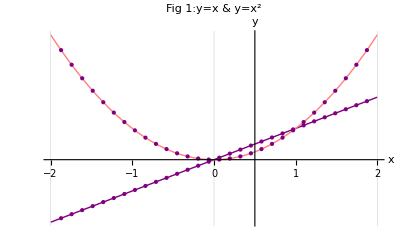

```mathematica
Plot[{x,x^2},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0},PlotStyle-> {Purple,Pink},PlotLegend-> {"x","x^2"},LegendPosition->{0.6,-0.2}]
```

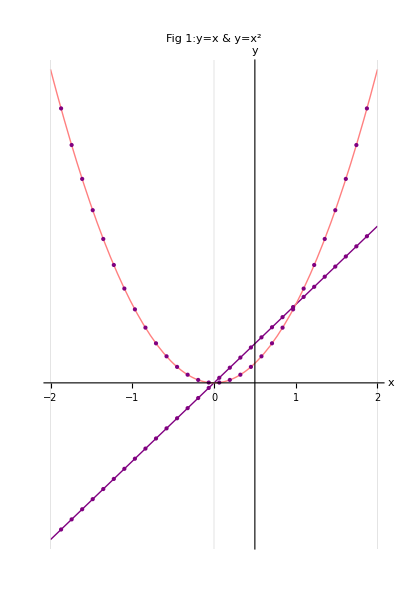

```mathematica
Plot[{x,x^2},{x,-2,2},Axes-> True,Frame-> False,Mesh-> 30,GridLines-> {{-2,2,0},None},Ticks-> {Automatic,None},PlotLabel-> "Fig 1:y=x & y=x^2",AxesLabel-> {"x","y"},AxesOrigin-> {0.5,0},PlotStyle-> {Purple,Pink},PlotLegend-> {"x","x^2"},LegendPosition->{0.6,-0.2},AspectRatio-> 1.5]
```

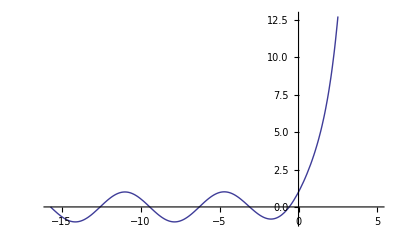

```mathematica
Plot[E^x+Sin[x],{x,-5π,5}]
```

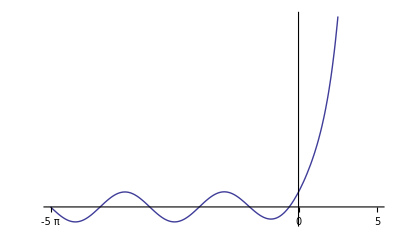

```mathematica
Plot[E^x+Sin[x],{x,-5π,5},Ticks-> {{-5π,0,5},None}]
```

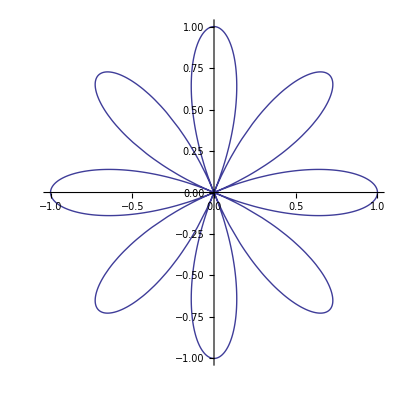

```mathematica
PolarPlot[Cos[4θ],{θ,0,2π}]
```

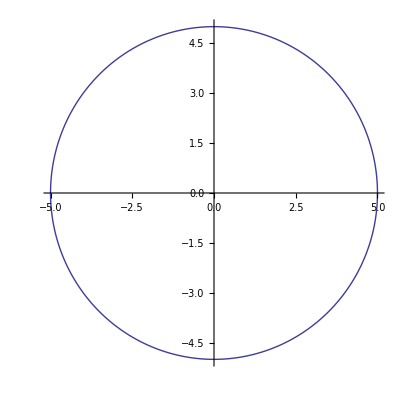

```mathematica
ParametricPlot[{5Cos[θ],5Sin[θ]},{θ,0,2π},AspectRatio-> 1]
```

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

```mathematica
ContourPlot3D[z==x^2+y^2,{x,-5,5},{y,-5,5},{z,0,3}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π},AxesLabel-> {"x","y","z"},Mesh-> None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{(x^2+y^2)},{x,0,2π},{y,0,2π},AxesLabel-> {"x","y","z"},PlotPoints->50]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{x^2+3 y^2,-(x^2+y^2)},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{x^2+y^2,-(x^2+y^2)},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Animate[Plot3D[Sin[x*y+50t],{x,0,2π},{y,0,2π},Mesh-> None,PlotPoints->50],{t,0,2π}]
```